```mathematica
InterpolatingPolynomial[{{{xjm1},0,0},{{xj},1,0}},x]
```

(-(2 (x-xj))/(xj-xjm1)^3+1/(xj-xjm1)^2) (x-xjm1)^2

```mathematica
Expand[(-(2 (x-xj))/h^3+1/h^2) (x-xjm1)^2]
```

x^2-2 x^3+2 x^2 xj-2 x xjm1+4 x^2 xjm1-4 x xj xjm1+xjm1^2-2 x xjm1^2+2 xj xjm1^2

```mathematica
InterpolatingPolynomial[{{{xjp1},0,0},{{xj},1,0}},x]
```

(-(2 (x-xj))/(xj-xjp1)^3+1/(xj-xjp1)^2) (x-xjp1)^2

```mathematica
Expand[((2 (x-xj))/h^3+1/h^2) (x-xjp1)^2]
```

x^2+2 x^3-2 x^2 xj-2 x xjp1-4 x^2 xjp1+4 x xj xjp1+xjp1^2+2 x xjp1^2-2 xj xjp1^2

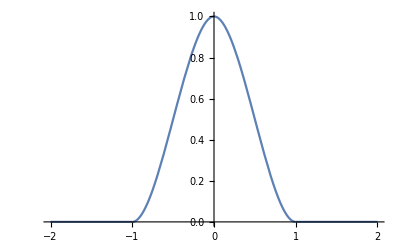

```mathematica
xjm1 = -1;
xj = 0;
xjp1 = 1;
h = 1;
phi1[x_]:=Piecewise[{{(-(2 (x-xj))/h^3+1/h^2) (x-xjm1)^2, xjm1<=x≤xj}, {((2 (x-xj))/h^3+1/h^2) (x-xjp1)^2, xj≤x≤xjp1}, {0, True}}]
Plot[phi1[x],{x,-2,2}]
```

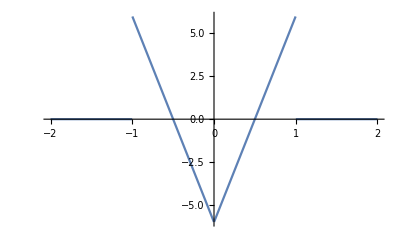

```mathematica
Plot[phi1''[x],{x,-2,2}]
```

```mathematica
Clear[h]
phi1''[x]
```

Piecewise[{{2 (1/h^2-(2 (x-xj))/h^3)-(8 (x-xjm1))/h^3, -x+xjm1≤0&&-x+xj≥0}, {2 (1/h^2+(2 (x-xj))/h^3)+(8 (x-xjp1))/h^3, -x+xj≤0&&-x+xjp1≥0}, {0, True}}]

```mathematica
Clear[xj,xjm1,xjp1]
```

```mathematica
InterpolatingPolynomial[{{{xjp1},0,0},{{xj},0,1}},x]
```

((x-xj) (x-xjp1)^2)/(xj-xjp1)^2

```mathematica
((x-xj) (x-xjp1)^2)/h^2
```

```mathematica
Expand[(-1+x)^2 x]
```

x-2 x^2+x^3

```mathematica
InterpolatingPolynomial[{{{xjm1},0,0},{{xj},0,1}},x]
```

((x-xj) (x-xjm1)^2)/(xj-xjm1)^2

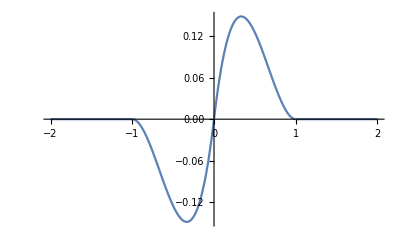

```mathematica
xjm1 = -1;
xj = 0;
xjp1 = 1;
h = 1;
phi2[x_]:=Piecewise[{{((x-xj) (x-xjm1)^2)/h^2, xjm1<=x≤xj}, {((x-xj) (x-xjp1)^2)/h^2, xj≤x≤xjp1}, {0, True}}]
Plot[phi2[x],{x,-2,2}]
```

```mathematica
Clear[xj,xjm1,xjp1]
phi2''[x]
```

Piecewise[{{2 (x-xj)+4 (x-xjm1), -x+xjm1≤0&&-x+xj≥0}, {2 (x-xj)+4 (x-xjp1), -x+xj≤0&&-x+xjp1≥0}, {0, True}}]

```mathematica
phi2''[x]
```

Piecewise[{{0, x<-1}, {4+6 x, -1<x<0}, {-4+6 x, 0<x<1}, {0, x>1}, {Indeterminate, True}}]

```mathematica
exactSol[x_]:=((18-2 π^2)x^2+(-24 - 4 π^2)x^3+(9+2 π^2)x^4)*Sin[2π x];
exactSol'[x]//Simplify
```

2 x (π x (2 π^2 (-1-2 x+x^2)+3 (6-8 x+3 x^2)) Cos[2 π x]+2 (9 (-1+x)^2+π^2 (-1-3 x+2 x^2)) Sin[2 π x])

```mathematica
exactSol''[x]//Simplify
```

16 π x (9 (-1+x)^2+π^2 (-1-3 x+2 x^2)) Cos[2 π x]-4 (2 π^4 x^2 (-1-2 x+x^2)-9 (1-4 x+3 x^2)+π^2 (1+6 x+12 x^2-24 x^3+9 x^4)) Sin[2 π x]